## Simple Particle Dynamics

### Initial Article

This source is taken from here (I have modified it for my understanding, but have not changed its function): https://mathematica.stackexchange.com/questions/161471/simulating-molecular-dynamics-efficiently

```mathematica
Needs["CCompilerDriver`"];Needs["Developer`"];$HistoryLength=10;<< CompiledFunctionTools`
```

```mathematica
CCompilers[]
```

{{Name→Visual Studio,Compiler→CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler,CompilerInstallation→C:\Program Files\Microsoft Visual Studio\2022\Community,CompilerName→Automatic}}

```mathematica
size=50.;(*size of the box*)
box={{-size,size},{-size,size}};
r0=1.(*diameter of one particle*);
Block[{r,x1,x2,y1,y2,xx,yy,force,potential},
(*xx & yy are each stand-ins for two dimensional vector.*)
xx={x1,x2};
yy={y1,y2};
potential=Function[r,1/4 ((r0/r)^2-(r0/r))];
force=-D[potential[Sqrt[Dot[xx-yy,xx-yy]]],{xx,1}];
With[
{f1code=N@force[[1]],f2code=N@force[[2]],slope=100.,  a1=N@box[[1,1]],b1=N@box[[1,2]],a2=N@box[[2,1]],b2=N@box[[2,2]]},(* All these N@s merely convert numbers to machine numbers. *)
(*This is the output: 
the symbol "getForces" becomes defined in the global environment. 
The Block and With protect symbols used to make the function.
Getforces will be passed a list of positions of particles nearest each particle.  Since it is listable, the function will iterate through the first level (i.e., particle by particle) and calculate the forces on each particle due to its nearest neighbors. *)
getForces=Compile[{{X,_Real,2}}, (* X is a list of particle positions. *)
Block[{x1,x2,y1,y2,f1,f2},x1=Compile`GetElement[X,1,1];
x2=Compile`GetElement[X,1,2];
f1=slope (Ramp[a1-x1]-Ramp[x1-b1]);
f2=slope (Ramp[a2-x2]-Ramp[x2-b2]);
Do[y1=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
f1+=f1code;
f2+=f2code;,{i,2,Length[X]}];
{f1,f2}],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True]]]
```

CompiledFunction[…]

```mathematica
step=Function[x, (* Below, the symbols h & m are protected by Function *)
(* Nearest will return a list the length of x of all the particle locations (thus, a list of two elements) within epsilon of each member of x. *)
(* h^2/m could be precomputed.*)
(xnew=2. x-xold+h^2 (1./m) getForces[Nearest[x,x,{∞,epsilon}]];
xold=x;
xnew)];
```

```mathematica
SeedRandom[1234];
n=200;(*number of particules*)
h=0.01;(*time step*)
epsilon=10.;(* radius of influence*)
(*initial conditions*) 
(* With size=50, starts at {-48,-50} ... {48,-50}, {-50, -49} ... {-48, -49}, and so on, oddly ending with {-50,46}.*)
x0=N@Table[{2 Mod[i,size]-size,Floor[i/50]-size},{i,n}];
v0=0.1 size RandomReal[{-1,1},{n,2}];
x1=x0+h v0;(*Initialize Verlet integration scheme*)
m(*particle masses*)=ConstantArray[1.,n ];
```

```mathematica
timesteps=10000;(* 10,000 in original.  Set to 1,000 to compare data to the speedup version,  would diverges starting around 400 steps.*)
xold=x0;
x=x1;
temp=AbsoluteTiming[data=Join[{x0},NestList[step,x1,timesteps]]];
to=temp⟦1⟧
```

3.84397

```mathematica
frames=Map[X↦Graphics[{PointSize[1/size],Point[X]},PlotRange->box,PlotRangePadding->0.1 size],data];
Animate[frames⟦i⟧,{i,1,Length[frames],20}]
```

```mathematica
Export["a.gif",frames[[1;;-1;;20]]]
```

a.gif

```mathematica
SystemOpen["a.gif"]
```

‘data’ is retained to compare it to later improvements.

```mathematica
ClearAll[x,x1,v0,x0,xold,xnew,xx,temp]
```

### Further Improvements

The same article had an improved version:

```mathematica
(* size=50.;(*size of the box*)box={{-size,size},{-size,size}};
r0=1.;*)(*diameter of one particle*)
Quiet[Block[{x1,x2,y1,y2,xx,yy,force,potential,r,r2},xx={x1,x2};
yy={y1,y2};
potential=r↦4 ((r0/r)^12-(r0/r)^6);
force=Simplify[-D[potential[Sqrt[Dot[xx-yy,xx-yy]]],{xx,1}]/.(x1-y1)^2+(x2-y2)^2->r2]/.Sqrt[r2]->r;
With[{f1code=N@force[[1]],f2code=N@force[[2]],slope=100.,a1=N@box[[1,1]],b1=N@box[[1,2]],a2=N@box[[2,1]],b2=N@box[[2,2]]},getStep=Compile[{{X,_Real,2},{Xold,_Real,1},{ilist,_Integer,1},{factor,_Real}},
(* X is passed as a 2 dim array. Xold and ilist are threaded, as they are really two dimensional.*)
Block[{x1,x2,y1,y2,f1,f2,r,r2,j,i},j=Compile`GetElement[ilist,1];
x1=Compile`GetElement[X,j,1];
x2=Compile`GetElement[X,j,2];
f1=slope (Ramp[a1-x1]-Ramp[x1-b1]);
f2=slope (Ramp[a2-x2]-Ramp[x2-b2]);
Do[i=Compile`GetElement[ilist,k];
y1=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
r2=(x1-y1)^2+(x2-y2)^2;
r=Sqrt[r2];
f1+=f1code;
f2+=f2code;,{k,2,Length[ilist]}];
{2. x1-Compile`GetElement[Xold,1]+factor f1,
2. x2-Compile`GetElement[Xold,2]+factor f2}],
CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"]]]];
```

```mathematica
SeedRandom[1234];
n=1000; (* much larger number of particles*)
h=0.005;(*time step*)
epsilon=3.;(*smaller radius of influence*)
(*initial conditions*)
x0=Developer`ToPackedArray[N@Table[{2 Mod[i,size]-size,Floor[i/50]-size},{i,n}]];
v0=0.1 size RandomReal[{-1,1},{n,2}];
x1=x0+h v0;

m=ConstantArray[1.,n];(*particle masses*)factors=(h^2./m);
timesteps=10000;
skip=10;(*Nearest gets called only every 10th time iteration*)
```

Main loop:

```mathematica
datai=ConstantArray[0.,{timesteps+1,n,2}];(* changed name to datai to retain original data *)
datai[[1]]=x0;
datai[[2]]=x1;
xold=x0;
x=x1;
ilists=Nearest[x->Automatic,x,{∞,epsilon}];
temp=AbsoluteTiming[Do[If[Mod[iter,skip]==0,ilists=Nearest[x->Automatic,x,{∞,epsilon}];];
datai[[iter]]=xnew=Developer`ToPackedArray[getStep[x,xold,ilists,factors]];
xold=x;
x=xnew;,{iter,3,timesteps+1}]];
ti=temp⟦1⟧
```

4.16273

So that was a bit longer, but with 1,000 particles instead of 200. 

We’ll make a plot function instead of the script in the post:

```mathematica
plotData[v0_,data_,h_,r0_:1,size_,skip_:1]:=(* Fixed missing square on v0 *)
Module[{velocities=Sqrt[(Join[{v0},Differences[data]/h]^2).ConstantArray[1.,{2}]],colorcoords,box={{-size,size},{-size,size}}},
colorcoords=Rescale[Clip[velocities,{-100,100}]];
Table[Graphics[{PointSize[0.5 r0/size],Transpose[{ColorData["TemperatureMap"]/@colorcoords[[i]],Point/@data[[i]]}]
},PlotRange->box,PlotRangePadding->0.1 size,Background->Black],
{i,1,Length[data],skip}]];
```

```mathematica
framesi=plotData[v0,datai,h,r0,size,20];
```

```mathematica
Share[]
```

3672904

```mathematica
Animate[framesi[[i]],{i,1,Length[framesi],1}]
```

That wasn’t really a fair test, as it was 1,000 particles, not 200, a different potential, and with a different epsilon.  While it would not affect computation time, the timestep was different too.

```mathematica
ClearAll[datai,x,x0,x1,xold,v0,ilists,framesi,temp]
```

```mathematica
Names["Global`*"]
```

{a1,a2,args,b1,b2,BitDepth,box,colorcoords,colorcoords$,colorcoords$7864,data,datai,dims,epsilon,f1,f1code,f2,f2code,factor,factors,factor$,force,frames,framesi,framesi2,framesr,FullScreenArea,getForces,getStep,h,i,ilist,ilists,ilist$,iter,i$4932,i$4932$$,i$7901,i$7901$$,i$$,j,k,m,n,plotData,potential,r,r0,r2,Raster3DBoxOptionsImageEditMode,RasterBoxOptionsImageEditMode,Resolution,ScreenArea,size,skip,slope,step,temp,ti,timesteps,to,v0,velocities,velocities$,velocities$7849,x,X,x0,x1,x2,xnew,xold,Xold,Xold$,xx,X$,y1,y2,yy}

#### Comparison to original

To compare to the original, we need to recast the entire function (to use the same potential).  We also had to remove the RunTimeOption “Speed”.

```mathematica
(* size=50.;(*size of the box*)
box={{-size,size},{-size,size}};
r0=1.;*)(*diameter of one particle*)
Block[{x1,x2,y1,y2,xx,yy,force,potential,r,r2},xx={x1,x2};
yy={y1,y2};
potential=Function[r,1/4 ((r0/r)^2-(r0/r))];
force=Simplify[-D[potential[Sqrt[Dot[xx-yy,xx-yy]]],{xx,1}]/.(x1-y1)^2+(x2-y2)^2->r2]/.Sqrt[r2]->r;
With[{f1code=N@force[[1]],f2code=N@force[[2]],slope=100.,a1=N@box[[1,1]],b1=N@box[[1,2]],a2=N@box[[2,1]],b2=N@box[[2,2]]},getStep1=Compile[{{X,_Real,2},{xold,_Real,1},{ilist,_Integer,1},{factor,_Real}},Block[{x1,x2,y1,y2,f1,f2,r,r2,j,i},j=Compile`GetElement[ilist,1];
x1=Compile`GetElement[X,j,1];
x2=Compile`GetElement[X,j,2];
f1=slope (Ramp[a1-x1]-Ramp[x1-b1]);
f2=slope (Ramp[a2-x2]-Ramp[x2-b2]);
Do[i=Compile`GetElement[ilist,k];
y1=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
r2=(x1-y1)^2+(x2-y2)^2;
r=Sqrt[r2];
f1+=f1code;
f2+=f2code;,{k,2,Length[ilist]}];
{2. x1-Compile`GetElement[xold,1]+factor f1,
2. x2-Compile`GetElement[xold,2]+factor f2}],
CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True(*,RuntimeOptions->"Speed"*)]]];
```

```mathematica
SeedRandom[1234];
n=200; (* number of particles*)
h=0.01;(* time step *)
epsilon=10.;(* radius of influence *)
(*initial conditions*)x0=Developer`ToPackedArray[N@Table[{2 Mod[i,size]-size,Floor[i/50]-size},{i,n}]];
v0=0.1 size RandomReal[{-1,1},{n,2}];
x1=x0+h v0;

m=ConstantArray[1.,n];(*particle masses*)
factors=(h^2./m);
timesteps=10000; (* Limit the number of steps *)
skip=1;(*Nearest gets called  every time iteration*)
```

```mathematica
?getStep1
```

Global`getStep1

getStep1=CompiledFunction[…]

Main loop:

```mathematica
datai2=ConstantArray[0.,{timesteps+2,n,2}];
datai2[[1]]=x0;
datai2[[2]]=x1;
xold=x0;
x=x1;
ilists=Nearest[x->Automatic,x,{∞,epsilon}];
temp=AbsoluteTiming[Do[If[Mod[iter,skip]==0,ilists=Nearest[x->Automatic,x,{∞,epsilon}];];
datai2[[iter]]=xnew=Developer`ToPackedArray[getStep1[x,xold,ilists,factors]];
xold=x;
x=xnew;,{iter,3,timesteps+2}]];
ti2=temp⟦1⟧
```

2.28854

```mathematica
to/ti2
```

1.67966

So that was a bit faster.  It does not appear that either function is run in parallel.

```mathematica
framesi2=plotData[v0,datai2,h,r0,size,1];
```

The two simulations look very close.

```mathematica
Animate[{i,frames⟦i⟧,framesi2[[i]]},{i,1,Length[frames],20}]
```

We can compare them element-by-element,

```mathematica
ddata=Norm/@(datai2-data);
```

The numerical errors start to accumulate as different particles make it inside epsilon..

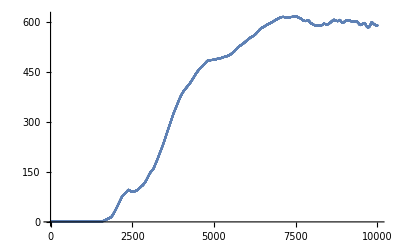

```mathematica
ListPlot[ddata]
```

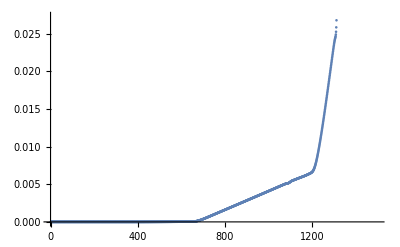

```mathematica
ListPlot[ddata⟦1;;1500⟧]
```

```mathematica
ClearAll[datai2,x0,x1,xold, x,framesi2,ddata,temp]
```

```mathematica
Share[]
```

1707216

## Renamed Variables

The variables had odd names, so I copied the above and started renaming variables.
xx, yy -> p1, p2 (we are calculating the force on point 1 by point 2)
x1, x2, y1, y2 -> x1, y1, x2, y2 for principle and i’th particle; x & y now refer to directions.  These symbols are reused.
f1code, f2code -> fxcode, fycode (directions)
a1, b1, a2, b2 -> bl, br, bb, bt (box left, right, bottom, top)
f1, f2 -> fx, fy

Within getForces,
x1, x2 -> xp, yp  (the principle point for which forces are being calculated)
y1, y2 -> xi, yi (the i’th point near principle point)

```mathematica
ClearAll[size,box,r0,step,n,h,epsilon,m];
size=50.;(*size of the box*)
box={{-size,size},{-size,size}};
r0=1.(*diameter of one particle*);
Block[{r,x1,x2,y1,y2,p1,p2,force,potential},
(*current & last are each stand-ins for two dimensional vector.*)
p1={x1,y1};
p2={x2,y2};
potential=Function[r,1/4 ((r0/r)^2-(r0/r))];
(* The subtraction need not be repeated. *)
(* 'force' will be a list of two elements, each the partial wrt the constituents of p1; {x1, y1}. *)
force=-D[potential[Sqrt[Dot[p1-p2,p1-p2]]],{p1,1}];
With[
{fxcode=N@force[[1]],fycode=N@force[[2]],slope=100.,  bl=N@box[[1,1]],br=N@box[[1,2]],bb=N@box[[2,1]],bt=N@box[[2,2]]},(* All these Ns merely convert numbers to machine numbers. *)
(*This is the output: 
the symbol "getForces" becomes defined in the global environment. 
The Block and With protect symbols used to make the function.
getForces will be passed the output of Nearest (see below), and since it is Listable, will be threadded over that list.  Thus, the input to getForces is a single list of the particles near particle i, whose location is first in the list (since its distance from itself is zero). *)
getForces=Compile[{{X,_Real,2}},Block[{x1,y1,x2,y2,fx,fy},
(* x1 & x2 have the x & y coordinate of particle i*)
x1=Compile`GetElement[X,1,1];
y1=Compile`GetElement[X,1,2];
(* f1 & f2 wil be the x & y forces on particle i.  This first claculation applies force from the walls, whichi are 'slope' times the distance past the edge of the walls. *)
fx=slope (Ramp[bl-x1]-Ramp[x1-br]);
fy=slope (Ramp[bb-y1]-Ramp[y1-bt]);
Do[x2=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
fx+=fxcode; (* 'fxcode' is an expression in terms of the symbols x1, y1, x2, & y2.*)
fy+=fycode;,{i,2,Length[X]}];
{fx,fy}],
CompilationTarget->"C",RuntimeAttributes->{Listable},
Parallelization->True,RuntimeOptions->"Speed"]]]
```

CompiledFunction[…]

```mathematica
step=Function[x,(* The Nearest call will return a list of n lists, list i containing a list of all the particle locations sorted by distance, starting with particle i itself (which has distance zero from itself).*)
(xnew=2. x-xold+h^2 (1./m) getForces[Nearest[x,x,{∞,epsilon}]];
xold=x;
xnew)];
```

```mathematica
SeedRandom[1234];
n=200;(*number of particles*)
h=0.01;(*time step*)
epsilon=10.;(*radius of influence*)
(*initial conditions*) 
(* With size=50, starts at {-48,-50} ... {48,-50}, {-50, -49} ... {-48, -49}, and so on, oddly ending with {-50,46}.*)
x0=N@Table[{2 Mod[i,size]-size,Floor[i/50]-size},{i,n}];
v0=0.1 size RandomReal[{-1,1},{n,2}];
x1=x0+h v0;(*Initialize Verlet integration scheme*)
m(*particle masses*)=ConstantArray[1.,n ];
```

```mathematica
timesteps=10000;
xold=x0;
x=x1;
temp=AbsoluteTiming[datar=Join[{x0},NestList[step,x1,timesteps]]];
tr=temp⟦1⟧
```

3.46531

```mathematica
tr/to
```

0.901492

```mathematica
framesr=plotData[v0,datar,h,r0,size,1];
```

```mathematica
Animate[{i,frames⟦i⟧,framesr⟦i⟧},{i,1,Length[framesr],20}]
```

This yielded the identical result.

```mathematica
ddatar=Norm/@(datar-data);
```

```mathematica
Max[ddatar]
```

0.

So the renamed version is identical to the original.

```mathematica
ClearAll[ddatar,x,x1,x0,xold,v0,datar,framesr,temp]
```

### Further Improvements

We’ll do the same renaming to the improved version.

```mathematica
size=50.;(*size of the box*)
box={{-size,size},{-size,size}};
r0=1.;(*diameter of one particle*)
Block[{x1,x2,y1,y2,p1,p2,force,potential,r,r2},p1={x1,y1};
p2={x2,y2};
potential=Function[r,1/4 ((r0/r)^2-(r0/r))];
force=Simplify[-D[potential[Sqrt[Dot[p1-p2,p1-p2]]],{p1,1}]/.(x1-x2)^2+(y1-y2)^2->r2]/.Sqrt[r2]->r;
With[{fxcode=N@force[[1]],fycode=N@force[[2]],slope=100.,bl=N@box[[1,1]],br=N@box[[1,2]],bb=N@box[[2,1]],bt=N@box[[2,2]]},getStep1r=Compile[{{X,_Real,2},{xold,_Real,1},{ilist,_Integer,1},{factor,_Real}},Block[{x1,x2,y1,y2,fx,fy,r,r2,j,i},j=Compile`GetElement[ilist,1];
x1=Compile`GetElement[X,j,1];
y1=Compile`GetElement[X,j,2];
fx=slope (Ramp[bl-x1]-Ramp[x1-br]);
fy=slope (Ramp[bb-y1]-Ramp[y1-bt]);
Do[i=Compile`GetElement[ilist,k];
x2=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
r2=(x1-x2)^2+(y1-y2)^2;
r=Sqrt[r2];
fx+=fxcode;
fy+=fycode;,{k,2,Length[ilist]}];
{2. x1-Compile`GetElement[xold,1]+factor fx,
2. y1-Compile`GetElement[xold,2]+factor fy}],
CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True(*,RuntimeOptions->"Speed"*)]]];
```

```mathematica
SeedRandom[1234];
n=200; (*number of particules*)
h=0.01;(*time step*)
epsilon=10.;(*radius of influence*)
(*initial conditions*)x0=Developer`ToPackedArray[N@Table[{2 Mod[i,size]-size,Floor[i/50]-size},{i,n}]];
v0=0.1 size RandomReal[{-1,1},{n,2}];
x1=x0+h v0;

m=ConstantArray[1.,n];(*particle masses*)
factors=(h^2./m);
timesteps=10000; (* Limit the number of steps *)
skip=1;(*Nearest gets called  every time iteration*)
```

Main loop:

```mathematica
datair=ConstantArray[0.,{timesteps+2,n,2}];
datair[[1]]=x0;
datair[[2]]=x1;
xold=x0;
x=x1;
ilists=Nearest[x->Automatic,x,{∞,epsilon}];
temp=AbsoluteTiming[Do[If[Mod[iter,skip]==0,ilists=Nearest[x->Automatic,x,{∞,epsilon}];];
datair[[iter]]=xnew=Developer`ToPackedArray[getStep1r[x,xold,ilists,factors]];
xold=x;
x=xnew;,{iter,3,timesteps+2}]]
tir=temp⟦1⟧
```

{2.07365,Null}

2.07365

```mathematica
{ti2/tir,ti2/to}
```

{1.10363,0.59536}

The renamed appear a bit faster than the original post.

The two simulations look very close.

```mathematica
framesir=plotData[v0,datair,h,r0,size,1];
```

```mathematica
Animate[{i,frames⟦i⟧,framesir[[i]]},{i,1,Length[framesir],20}]
```

We can compare them element-by-element.

```mathematica
ddatair=Norm/@(datair-data);
```

We get the same results as the improved version.

```mathematica
ListPlot[ddatair]
```

-Graphics-

```mathematica
ListPlot[ddatair⟦1;;1500⟧]
```

-Graphics-

```mathematica
ClearAll[datair,x,x1,x0,xold,xnew,v0,ddatair,temp]
```

```mathematica
Share[]
```

1060960

## Getting Production Code

The code above uses parameters from the environment in several different ways, and these all need to be regularized.  The target is to be able to save a configuration to a file, and continue the simulation by reading the data from a file and adding more steps, possibly with some changes.

The parameters come in a few flavors.  Some are essentially hardwired into the compiled code, specifically the box size and shape,  and the potential function is also hardwired.  Also, the symbol in which the compiled function is contained is in the OwnValues of a symbol declared in the code. 

Below we make the compiled function creation a function of those  parameters, and also of the potential function.

```mathematica
createStepFn[potential_,size_Real:50.0,boxRatio_Real:1.0]:=
(*size is double the x side of the box, boxRatio is the multiplier of the y side. *)
 Module[ {box={{-size,size},boxRatio{-size,size}}},  (* r0=1.; diameter of one particle*)
  Block[{x1,x2,y1,y2,p1,p2,force,r,r2},
p1={x1, y1};p2={x2, y2};force=Simplify[-D[potential[Sqrt[Dot[p1-p2,p1-p2]]],{p1,1}]/.(x1-x2)^2+(y1-y2)^2->r2]/.Sqrt[r2]->r;With[{fxcode=N@force[[1]], fycode=N@force[[2]],slope=100.,bl=N@box[[1,1]],br=N@box[[1,2]],bb=N@box[[2,1]],bt=N@box[[2,2]]}, Compile[{{X,_Real, 2},{xold,_Real,1},{ilist,_Integer,1},{factor,_Real}}, 
(* X is passed as a full 2 dimensional array. 
Xold and ilist are threaded, as they are really two dimensional.*)Block[{x1,x2,y1,y2,fx,fy,r,r2,j,i},
j=Compile`GetElement[ilist,1];
x1=Compile`GetElement[X,j,1];
y1=Compile`GetElement[X,j,2];fx=slope(Ramp[bl-x1]-Ramp[x1-br]);fy=slope(Ramp[bb-y1]-Ramp[y1-bt]);Do[i=Compile`GetElement[ilist,k];x2=Compile`GetElement[X,i,1];y2=Compile`GetElement[X,i,2];r2=(x1-x2)^2+(y1-y2)^2;r=Sqrt[r2];fx+=fxcode;fy+=fycode;,
{k,2,Length[ilist]}];
{2.x1-Compile`GetElement[xold, 1]+factor fx,
2.y1-Compile`GetElement[xold,2]+factor fy}],
CompilationTarget -> "C", RuntimeAttributes -> {Listable}, Parallelization -> True, RuntimeOptions -> "Quality"]]]]
```

```mathematica
potential=1/4 ((1/#)^2-(1/#))&
```

1/4 ((1/#1)^2-1/#1)&

```mathematica
getStep2=createStepFn[potential,50.0]
```

CompiledFunction[…]

We need to create the initial system state:

```mathematica
initState[n_Integer,h_,epsilon_,m_,stepFun_,skip_,size_,boxratio_]:=Module[{x0=Developer`ToPackedArray[N@Table[{2 Mod[i,size]-size,Floor[i/size]-size},{i,n}]],v0=0.1 size RandomReal[{-1,1},{n,2}]},
<|"n"->n,(*number of particules*)
"h"->h,(*time step*)
"epsilon"->epsilon,(*radius of influence*)
"m"->m,(* Particle mass *)
"stepFun"->stepFun,(* Try to store in data. *)
"skip"->skip,(* The number of steps between Nearest calls *)
"size"->size,
"boxratio"->boxratio,
"x0"->x0,
"v0"->v0|>]
```

```mathematica
SeedRandom[1234];
ss=initState[200,0.01,10,1.0,getStep2,1,50.0,1.0];
```

The state include positions and velocities, so we would like to see the state without those values.

```mathematica
printState[ss_Association]:=Print[KeyDrop[ss,{"x0","v0"}],Dimensions[ss["x0"]],Dimensions[ss["v0"]]]
```

```mathematica
printState[ss]
```

<|n→200,h→0.01,epsilon→10,m→1.,stepFun→CompiledFunction[…],skip→1,size→50.,boxratio→1.|>{200,2}{200,2}

A function to run the code will be convenient too.

```mathematica
execSteps[ timesteps_Integer,ss_Association]:=Module[
{n=ss["n"],h=ss["h"],epsilon=ss["epsilon"],m=ss["m"],factors=ss["h"]^2/ss["m"],x0=ss["x0"],x1=ss["x0"]+ss["h"] ss["v0"], xold=ss["x0"],x,xnew,v0=ss["v0"],skip=ss["skip"],data=Developer`ToPackedArray[ConstantArray[0.,{timesteps+2,ss["n"],2}]],ilists,ssr=ss},
(*ilists=Nearest[x->"Index",x,{∞,epsilon}];*)
data⟦1⟧=x0;
data⟦2⟧=x1;
x=x1;
Do[If[Mod[iter,skip]==0,ilists=Nearest[x->"Index",x,{∞,epsilon}];];
data⟦iter+3⟧=xnew=Developer`ToPackedArray[ss["stepFun"][x,xold,ilists,factors]];
xold=x;
x=xnew;,{iter,0,timesteps-1}];
ssr["x0"]=Last[data];
ssr["v0"]=(data⟦timesteps+2⟧-data⟦timesteps+1⟧)/ss["h"];
{ssr,data}]
```

Execute the code:

```mathematica
temp=AbsoluteTiming[t=execSteps[10000,ss]];
```

```mathematica
tp=temp⟦1⟧
```

2.21173

```mathematica
tp/to
```

2.21173/to

```mathematica
printState[t⟦1⟧]
```

<|n→200,h→0.01,epsilon→10,m→1.,stepFun→CompiledFunction[…],skip→1,size→50.,boxratio→1.|>{200,2}{200,2}

```mathematica
Length[t⟦2⟧]
```

10002

```mathematica
Length[data]
```

0

```mathematica
ddata=t⟦2⟧-data;
```

The numerical errors still accumulate.

```mathematica
(* ddata=datan-data;*)
```

```mathematica
ListPlot[Norm/@ddata]
```

$Aborted

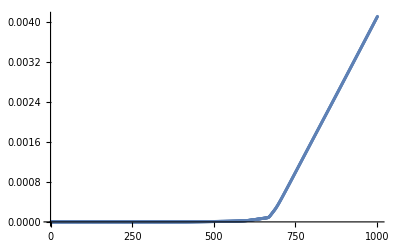

```mathematica
ListPlot[Norm/@ddata⟦1;;1002⟧]
```

If we increase the skip size it will increase the error

```mathematica
ss2=ss;ss2["skip"]=2;
ts=execSteps[1000,ss2];//AbsoluteTiming
```

{0.185517,Null}

```mathematica
ddata=ts⟦2⟧-data⟦1;;1002⟧;
```

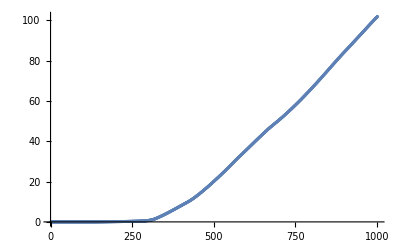

```mathematica
ListPlot[Norm/@ddata]
```

```mathematica
ssr=t⟦1⟧;
```

```mathematica
printState[ssr]
```

<|n→200,h→0.01,epsilon→10,m→1.,stepFun→CompiledFunction[…],skip→1,size→50.,boxratio→1.|>{200,2}{200,2}

We can now extend the run from where the last one left off.

```mathematica
Length[t⟦2⟧]
```

10002

```mathematica
tt=execSteps[1000,ssr];
```

```mathematica
trans=Join[t[[2]],tt⟦2⟧];
```

```mathematica
Length[trans]
```

11004

```mathematica
?plotData
```

Global`plotData

plotData[v0_,data_,h_,r0_:1,size_,skip_:1]:=Module[{velocities=√(Join[{v0},Differences[data]/h]^2.ConstantArray[1.,{2}]),colorcoords},colorcoords=Rescale[Clip[velocities,{-100,100}]];Table[Graphics[{PointSize[(0.5 r0)/size],Transpose[{ColorData[TemperatureMap]/@colorcoords⟦i⟧,Point/@data⟦i⟧}]},PlotRange→box,PlotRangePadding→0.1 size,Background→Black],{i,1,Length[data],skip}]]

```mathematica
framesp=plotData[ss["v0"],trans,ssr["h"],1,ssr["size"],1];
```

```mathematica
Animate[{i,framesp[[i]]},{i,1,Length[framesp],1}]
```

```mathematica
ClearAll[ddata,temp,t,tt]
```

```mathematica
ssr["v0"]
```

{{-0.050493,0.00424143},{0.015876,0.0463431},{-0.0238317,-0.0103388},{0.0416279,-0.00854258},{0.0367794,-0.0333106},{-0.0250022,0.0340874},{-0.0123891,-0.00961325},{0.00780757,-0.0134634},{-0.00415961,-0.00648315},{0.017902,-0.0153696},{0.00727177,-0.0152298},{0.00117273,0.00700171},{-0.0396745,-0.0259503},{-0.0224712,-0.017121},{0.0249752,-0.0248376},{-0.00776474,0.0140912},{-0.0550928,0.00239975},{-0.00352684,-0.0166997},{0.0346406,-0.0443421},{-0.0321337,0.0174112},{-0.0145373,0.015733},{-0.0272815,-0.0473737},{-0.0223695,-0.0108687},{-0.07154,-0.0137829},{0.0103386,-0.00325503},{0.0475,-0.0267857},{0.0183365,-0.00100916},{0.015277,0.0537566},{-0.0240214,-0.00641806},{-0.0199479,0.00311514},{-0.0241473,0.0162729},{0.0420333,-0.0511133},{-0.00655982,0.0610793},{0.0442394,0.00312602},{0.0656047,-0.0111831},{-0.0301049,0.0349681},{-0.00963676,0.022929},{0.029951,0.0107642},{0.0132195,0.0234271},{-0.00608366,0.0419229},{0.00980719,0.0151004},{0.0200029,-0.0378067},{-0.033609,-0.00481582},{0.0026375,-0.023403},{-0.0133155,-0.0112189},{0.0196638,-0.0656205},{-0.00600114,-0.0137696},{0.0133817,0.0296936},{-0.0242594,-0.0293121},{-0.0213833,0.0227055},{-0.000895678,-0.0439116},{-0.0286853,-0.031643},{0.0383256,0.00665801},{-0.0183305,-0.0181752},{0.0565489,-0.0724033},{0.0259373,0.0391081},{0.029099,0.0111353},{-0.00286699,0.0071118},{-0.0121587,-0.0869506},{-0.017501,-0.0232331},{0.0108735,-0.0350797},{0.0327274,0.00275523},{0.0220654,-0.00106261},{0.0341773,-0.0000865091},{-0.0111046,0.0405393},{-0.00529718,-0.0134735},{-0.0233427,0.00718314},{-0.0176348,-0.0169629},{-0.00613803,0.0643131},{0.00325101,-0.0116295},{0.0229929,-0.00610407},{0.00239729,0.00551792},{-0.0184718,-0.0356269},{-0.0494113,0.0214831},{0.0110685,0.0656412},{0.00739426,0.0283111},{-0.00426585,-0.00678853},{0.0112765,-0.00691507},{0.00822055,0.0219679},{0.0210189,0.0278134},{0.0119362,-0.000949416},{0.0668044,-0.0386232},{0.0504799,0.00490617},{-0.0172523,-0.0172159},{-0.0270327,-0.0161972},{0.0535183,0.0533603},{-0.0392687,0.0268011},{0.0230809,0.0237377},{0.00788572,0.040803},{0.0149046,0.0340523},{0.0256013,-0.0613998},{0.0343714,-0.0160935},{0.0239898,0.0683384},{-0.0340293,-0.0297343},{0.0142073,0.0371781},{-0.0166203,0.0127372},{-0.0333379,-0.0107737},{0.0190195,0.0659206},{-0.0411801,0.00953444},{0.0501289,-0.0214941},{0.0297447,-0.0640427},{-0.00743176,0.0361123},{-0.00760594,0.0124972},{0.034088,-0.0634872},{0.00415328,-0.0232704},{-0.0195239,-0.0154971},{0.0998712,-0.0410158},{-0.00358912,0.0413999},{-0.00604925,-0.00826225},{-0.0595356,0.00939268},{0.000766021,0.0303921},{0.0204802,-0.0342764},{-0.0354524,-0.00070677},{-0.03065,-0.00966088},{-0.0240756,-0.0151334},{-0.0323802,0.00775211},{0.0722745,-0.0538891},{0.0178751,-0.00205938},{-0.00997731,0.0108258},{-0.0110843,-0.0158679},{0.0201701,0.0148772},{-0.0252555,0.0100699},{0.0192967,-0.0326417},{0.0134588,0.0243859},{-0.00775067,0.0137171},{0.0156879,-0.0176571},{-0.00996395,0.00893424},{0.00524179,-0.0258398},{-0.027701,0.00436713},{0.0234183,-0.0129274},{0.00726575,0.00148334},{0.0390767,0.00433713},{0.0104173,0.0103435},{-0.0285716,-0.0890189},{-0.0130453,-0.0184038},{-0.0489989,0.0303748},{-0.0478171,-0.0169606},{-0.00579768,0.030382},{-0.0653449,0.0072587},{0.0349278,0.0468545},{0.0210163,0.0251578},{0.029914,-0.0322706},{0.0240546,-0.0401933},{0.002321,0.00731849},{0.00983052,0.00338461},{0.0181824,-0.0151097},{0.0358963,0.00463135},{-0.0254756,0.0225883},{-0.0650659,-0.0400162},{-0.000616361,-0.0122386},{-0.0281833,-0.00953325},{0.0466337,0.0000548193},{0.0268038,0.022228},{0.043573,0.0138249},{0.0309843,0.00650915},{-0.00621612,0.056216},{-0.0546952,0.0491965},{0.00582956,0.00809303},{-0.0728422,0.0430405},{-0.0120036,-0.0344247},{-0.00874662,-0.0297631},{-0.00372177,-0.0158773},{0.00455322,-0.0193038},{0.0159393,0.0200705},{-0.0198292,0.0221829},{-0.0184797,0.00330782},{-0.0323654,-0.0214156},{0.0131616,-0.00321681},{0.0326756,-0.0105914},{-0.0831257,-0.0211687},{-0.0197921,0.0261976},{-0.0483654,-0.0361299},{0.00984712,0.0374193},{-0.00179633,0.0126742},{0.0639762,-0.00163633},{0.0408002,-0.0550868},{0.025366,0.000696189},{0.0150394,0.0563406},{0.0499881,0.0079862},{-0.0291662,-0.00873671},{-0.0220352,-0.0497545},{0.00278673,-0.0044565},{0.0178381,-0.0148626},{0.000465688,0.0249863},{0.017421,-0.0570624},{-0.000377119,-0.0154558},{0.0303468,0.0510748},{-0.00812052,0.00334771},{-0.0179372,0.000446544},{0.0284674,0.00256034},{-0.0615079,-0.0175539},{0.00103161,0.0404273},{0.011244,0.0289884},{-0.00846502,0.05713},{0.00316586,-0.0483253},{-0.00793887,0.00583998},{-0.0412102,0.0138286},{0.0082456,0.0113779},{-0.0124031,0.0253271},{0.0325413,-0.0222147}}

## Playground

```mathematica
OwnValues[getStep1]
```

{HoldPattern[getStep1]:>CompiledFunction[…]}

```mathematica
Sin@Pi
```

```mathematica
ClearAll[r,x1,x2,y1,y2,xx,yy,force,potential]
```

```mathematica
xx={x1,x2};
yy={y1,y2};potential=Function[r,1/4 ((r0/r)^2-(r0/r))];
force=-D[potential[Sqrt[Dot[xx-yy,xx-yy]]],{xx,1}];
```

```mathematica
N@force⟦1⟧
```

0.25 ((2. (x1-1. y1))/(((x1-1. y1)^2+(x2-1. y2)^2)^2)-(1. (x1-1. y1))/(((x1-1. y1)^2+(x2-1. y2)^2)^(3/2)))

```mathematica
force[[2]]
```

1/4 ((2. (x2-y2))/(((x1-y1)^2+(x2-y2)^2)^2)-(1. (x2-y2))/(((x1-y1)^2+(x2-y2)^2)^(3/2)))

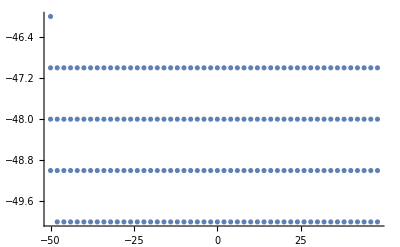

```mathematica
ListPlot[x0]
```

```mathematica
x0
```

{{-48.,-50.},{-46.,-50.},{-44.,-50.},{-42.,-50.},{-40.,-50.},{-38.,-50.},{-36.,-50.},{-34.,-50.},{-32.,-50.},{-30.,-50.},{-28.,-50.},{-26.,-50.},{-24.,-50.},{-22.,-50.},{-20.,-50.},{-18.,-50.},{-16.,-50.},{-14.,-50.},{-12.,-50.},{-10.,-50.},{-8.,-50.},{-6.,-50.},{-4.,-50.},{-2.,-50.},{0.,-50.},{2.,-50.},{4.,-50.},{6.,-50.},{8.,-50.},{10.,-50.},{12.,-50.},{14.,-50.},{16.,-50.},{18.,-50.},{20.,-50.},{22.,-50.},{24.,-50.},{26.,-50.},{28.,-50.},{30.,-50.},{32.,-50.},{34.,-50.},{36.,-50.},{38.,-50.},{40.,-50.},{42.,-50.},{44.,-50.},{46.,-50.},{48.,-50.},{-50.,-49.},{-48.,-49.},{-46.,-49.},{-44.,-49.},{-42.,-49.},{-40.,-49.},{-38.,-49.},{-36.,-49.},{-34.,-49.},{-32.,-49.},{-30.,-49.},{-28.,-49.},{-26.,-49.},{-24.,-49.},{-22.,-49.},{-20.,-49.},{-18.,-49.},{-16.,-49.},{-14.,-49.},{-12.,-49.},{-10.,-49.},{-8.,-49.},{-6.,-49.},{-4.,-49.},{-2.,-49.},{0.,-49.},{2.,-49.},{4.,-49.},{6.,-49.},{8.,-49.},{10.,-49.},{12.,-49.},{14.,-49.},{16.,-49.},{18.,-49.},{20.,-49.},{22.,-49.},{24.,-49.},{26.,-49.},{28.,-49.},{30.,-49.},{32.,-49.},{34.,-49.},{36.,-49.},{38.,-49.},{40.,-49.},{42.,-49.},{44.,-49.},{46.,-49.},{48.,-49.},{-50.,-48.},{-48.,-48.},{-46.,-48.},{-44.,-48.},{-42.,-48.},{-40.,-48.},{-38.,-48.},{-36.,-48.},{-34.,-48.},{-32.,-48.},{-30.,-48.},{-28.,-48.},{-26.,-48.},{-24.,-48.},{-22.,-48.},{-20.,-48.},{-18.,-48.},{-16.,-48.},{-14.,-48.},{-12.,-48.},{-10.,-48.},{-8.,-48.},{-6.,-48.},{-4.,-48.},{-2.,-48.},{0.,-48.},{2.,-48.},{4.,-48.},{6.,-48.},{8.,-48.},{10.,-48.},{12.,-48.},{14.,-48.},{16.,-48.},{18.,-48.},{20.,-48.},{22.,-48.},{24.,-48.},{26.,-48.},{28.,-48.},{30.,-48.},{32.,-48.},{34.,-48.},{36.,-48.},{38.,-48.},{40.,-48.},{42.,-48.},{44.,-48.},{46.,-48.},{48.,-48.},{-50.,-47.},{-48.,-47.},{-46.,-47.},{-44.,-47.},{-42.,-47.},{-40.,-47.},{-38.,-47.},{-36.,-47.},{-34.,-47.},{-32.,-47.},{-30.,-47.},{-28.,-47.},{-26.,-47.},{-24.,-47.},{-22.,-47.},{-20.,-47.},{-18.,-47.},{-16.,-47.},{-14.,-47.},{-12.,-47.},{-10.,-47.},{-8.,-47.},{-6.,-47.},{-4.,-47.},{-2.,-47.},{0.,-47.},{2.,-47.},{4.,-47.},{6.,-47.},{8.,-47.},{10.,-47.},{12.,-47.},{14.,-47.},{16.,-47.},{18.,-47.},{20.,-47.},{22.,-47.},{24.,-47.},{26.,-47.},{28.,-47.},{30.,-47.},{32.,-47.},{34.,-47.},{36.,-47.},{38.,-47.},{40.,-47.},{42.,-47.},{44.,-47.},{46.,-47.},{48.,-47.},{-50.,-46.}}

```mathematica
box
```

{{-50.,50.},{-50.,50.}}

```mathematica
t=Nearest[x0,x0,{∞,epsilon}];
```

```mathematica
Length[t]
```

200

```mathematica
Dimensions[t]
```

{200}

```mathematica
t⟦1⟧
```

{{-48.,-50.},{-48.,-49.},{-46.,-50.},{-48.,-48.},{-50.,-49.},{-46.,-49.},{-50.,-48.},{-46.,-48.},{-48.,-47.},{-50.,-47.},{-46.,-47.},{-44.,-50.},{-44.,-49.},{-44.,-48.},{-50.,-46.},{-44.,-47.},{-42.,-50.},{-42.,-49.},{-42.,-48.},{-42.,-47.},{-40.,-50.},{-40.,-49.},{-40.,-48.},{-40.,-47.},{-38.,-50.}}

```mathematica
t⟦2⟧
```

{{-46.,-50.},{-46.,-49.},{-48.,-50.},{-44.,-50.},{-46.,-48.},{-48.,-49.},{-44.,-49.},{-48.,-48.},{-44.,-48.},{-46.,-47.},{-48.,-47.},{-44.,-47.},{-42.,-50.},{-50.,-49.},{-42.,-49.},{-50.,-48.},{-42.,-48.},{-50.,-47.},{-42.,-47.},{-50.,-46.},{-40.,-50.},{-40.,-49.},{-40.,-48.},{-40.,-47.},{-38.,-50.},{-38.,-49.},{-38.,-48.},{-38.,-47.},{-36.,-50.}}

```mathematica
size=50.;(*size of the box*)
box={{-size,size},{-size,size}};
r0=1.(*diameter of one particle*);
Block[{r,x1,x2,y1,y2,xx,yy,force,potential},
(*xx & yy are each stand-ins for two dimensional vector.*)
xx={x1,x2};
yy={y1,y2};
potential=Function[r,1/4 ((r0/r)^2-(r0/r))];
force=-D[potential[Sqrt[Dot[xx-yy,xx-yy]]],{xx,1}];
With[
{f1code=N@force[[1]],f2code=N@force[[2]],slope=100.,  a1=N@box[[1,1]],b1=N@box[[1,2]],a2=N@box[[2,1]],b2=N@box[[2,2]]},(* All these Ns merely convert numbers to machine numbers. *)

(*This is the output: 
the symbol "getForces" becomes defined in the global environment. 
The Block and With protect symbols used to make the function.
Getforces will be passed a list of positions of particles nearest each particle.  Since it is listable, the function will iterate through the first level (i.e., particle by particle) and calculate the forces on each particle due to its nearest neighbors. *)
getForcesnc=Function[X, (* X is a list of particle positions. *)
Block[{x1,x2,y1,y2,f1,f2},x1=X⟦1,1⟧;
x2=X⟦1,2⟧;
f1=slope (Ramp[a1-x1]-Ramp[x1-b1]);
f2=slope (Ramp[a2-x2]-Ramp[x2-b2]);
Do[y1=Compile`GetElement[X,i,1];
y2=Compile`GetElement[X,i,2];
f1+=f1code;
f2+=f2code;,{i,2,Length[X]}];
{f1,f2}]]]]
```

Function[X$,Block[{x1,x2,y1,y2,f1,f2},x1=X$⟦1,1⟧;x2=X$⟦1,2⟧;f1=100. (Ramp[-50.-x1]-Ramp[x1-50.]);f2=100. (Ramp[-50.-x2]-Ramp[x2-50.]);Do[y1=Compile`GetElement[X$,i,1];y2=Compile`GetElement[X$,i,2];f1+=0.25 ((2. (x1-1. y1))/(((x1-1. y1)^2+(x2-1. y2)^2)^2)-(1. (x1-1. y1))/(((x1-1. y1)^2+(x2-1. y2)^2)^(3/2)));f2+=0.25 ((2. (x2-1. y2))/(((x1-1. y1)^2+(x2-1. y2)^2)^2)-(1. (x2-1. y2))/(((x1-1. y1)^2+(x2-1. y2)^2)^(3/2)));,{i,2,Length[X$]}];{f1,f2}]]

```mathematica
getForcesnc[Nearest[x0,x0⟦1⟧,{∞,epsilon}]]
```

{0.052651,-0.188322}

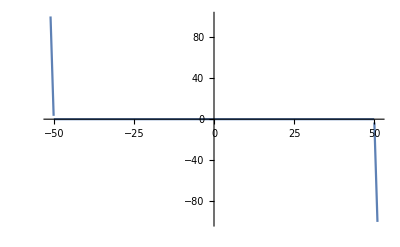

```mathematica
With[{slope=100, bl=-50,br=50},Plot[slope (Ramp[bl-x1]-Ramp[x1-br]),{x1,-51,51}]]
```

```mathematica
cP=Compile[{{x}},
Module[{sum=1.0,inc=1.0},Do[inc=inc*x/i;sum=sum+inc,{i,100000}];sum*x],
RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"];
arg=Range[ -50.,50, 0.01];
cP[arg];//AbsoluteTiming

cP2=Compile[{{x}},
Module[{sum=1.0,inc=1.0},Do[inc=inc*x/i;sum=sum+inc,{i,100000}];sum*x],
RuntimeAttributes->{Listable},Parallelization->False,CompilationTarget->"C"];
cP2[arg];//AbsoluteTiming
```

{0.397341,Null}

{1.14253,Null}

```mathematica
Length[arg]
```

5001

```mathematica
ClearAll[cP,cP2,arg]
```

{1.33936,Null}